# IGraph/M

## use igraph from Mathematica

This notebook can (and should) be opened using the command IGDocumentation[]. This notebook cannot be saved, so feel free to re-evaluate cells and experiment.

The documentation is currently incompete.  Contributions are welcome.

## Basic usage

The package can be loaded using

```mathematica
<<IGraphM`
```

This is the list of functions included. Notice that their names always have the IG prefix. Click on the name of a function to see its usage message.

```mathematica
?IGraphM`*
```

IGVersion[] returns the version of the igraph library in use.

```mathematica
IGVersion[]
```

IGraph/M 0.1.1dev
igraph 0.8.0-pre+1f7c4ea (Sep  8 2015)
Mac OS X x86 (64-bit)

IGraph/M functions work directly with Mathematica’s builtin Graph datatype. No new special graph datatype is introduced.

Let’s take a look at a few examples.

Let us first generate a graph using the builtin functions of Mathematica.

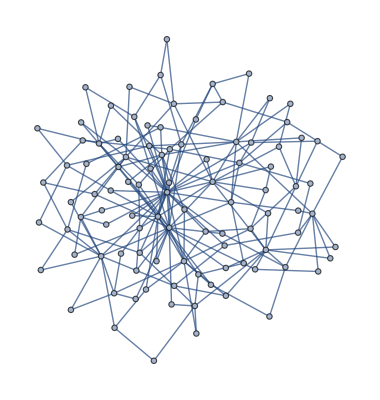

```mathematica
g=RandomGraph[BarabasiAlbertGraphDistribution[100,2]]
```

We can compute the betweenness centrality of each vertex using IGraph/M ...

```mathematica
IGBetweenness[g]
```

{1814.9,1006.96,757.609,572.712,237.306,62.5252,411.557,423.465,108.087,39.737,289.338,242.602,0.,16.6141,136.502,497.156,67.9986,368.25,84.1367,115.368,73.1454,255.46,152.945,14.3635,33.4879,24.4135,8.39167,43.3693,99.6936,55.1735,61.8088,37.5913,16.3644,15.2574,47.0286,118.185,134.419,0.,8.60536,0.,36.2341,50.7663,0.,7.11795,32.9729,77.7307,83.3629,93.7376,6.76485,23.6353,74.0362,51.7027,83.9491,5.78333,126.002,8.55392,9.71935,41.3762,5.75,38.7615,4.28333,10.661,70.6905,121.967,8.9901,209.604,5.93187,10.9509,21.1266,71.213,11.1766,14.3635,12.0405,6.85833,10.7808,4.5218,8.63313,22.8919,24.3667,26.8164,10.1588,0.,20.4971,0.,31.4932,16.3012,17.8944,7.99011,8.82857,0.,7.07222,10.1588,7.78333,6.91667,58.4839,16.1,34.3601,7.81667,3.87381,15.9119}

... or using Mathematica, and obtain the same result.

```mathematica
BetweennessCentrality[g]
```

{1814.9,1006.96,757.609,572.712,237.306,62.5252,411.557,423.465,108.087,39.737,289.338,242.602,0.,16.6141,136.502,497.156,67.9986,368.25,84.1367,115.368,73.1454,255.46,152.945,14.3635,33.4879,24.4135,8.39167,43.3693,99.6936,55.1735,61.8088,37.5913,16.3644,15.2574,47.0286,118.185,134.419,0.,8.60536,0.,36.2341,50.7663,0.,7.11795,32.9729,77.7307,83.3629,93.7376,6.76485,23.6353,74.0362,51.7027,83.9491,5.78333,126.002,8.55392,9.71935,41.3762,5.75,38.7615,4.28333,10.661,70.6905,121.967,8.9901,209.604,5.93187,10.9509,21.1266,71.213,11.1766,14.3635,12.0405,6.85833,10.7808,4.5218,8.63313,22.8919,24.3667,26.8164,10.1588,0.,20.4971,0.,31.4932,16.3012,17.8944,7.99011,8.82857,0.,7.07222,10.1588,7.78333,6.91667,58.4839,16.1,34.3601,7.81667,3.87381,15.9119}

Let us now assign weights to the edges. Many IGraph/M functions, including IGBetweenness, support edge weights.

```mathematica
wg=SetProperty[g,EdgeWeight->RandomReal[1,EdgeCount[g]]];
```

```mathematica
IGBetweenness[wg]
```

{2723.,1830.,431.,417.,79.,17.,401.,728.,62.,9.,357.,719.,0.,0.,156.,1153.,111.,439.,1058.,1.,94.,438.,8.,0.,31.,217.,0.,0.,31.,119.,36.,77.,68.,0.,145.,186.,46.,0.,5.,0.,7.,17.,0.,0.,3.,68.,345.,221.,0.,1.,34.,32.,42.,0.,114.,4.,0.,30.,0.,27.,0.,0.,192.,73.,0.,285.,42.,50.,0.,156.,0.,135.,0.,0.,12.,0.,0.,0.,0.,0.,6.,0.,67.,258.,94.,8.,4.,0.,0.,0.,0.,0.,90.,0.,225.,0.,0.,0.,554.,122.}

Notice that Mathematica 10.2 does not include functionality to compute weighted betweenness. BetweennessCentrality[] ignores the weights.

```mathematica
BetweennessCentrality[wg]
```

{1814.9,1006.96,757.609,572.712,237.306,62.5252,411.557,423.465,108.087,39.737,289.338,242.602,0.,16.6141,136.502,497.156,67.9986,368.25,84.1367,115.368,73.1454,255.46,152.945,14.3635,33.4879,24.4135,8.39167,43.3693,99.6936,55.1735,61.8088,37.5913,16.3644,15.2574,47.0286,118.185,134.419,0.,8.60536,0.,36.2341,50.7663,0.,7.11795,32.9729,77.7307,83.3629,93.7376,6.76485,23.6353,74.0362,51.7027,83.9491,5.78333,126.002,8.55392,9.71935,41.3762,5.75,38.7615,4.28333,10.661,70.6905,121.967,8.9901,209.604,5.93187,10.9509,21.1266,71.213,11.1766,14.3635,12.0405,6.85833,10.7808,4.5218,8.63313,22.8919,24.3667,26.8164,10.1588,0.,20.4971,0.,31.4932,16.3012,17.8944,7.99011,8.82857,0.,7.07222,10.1588,7.78333,6.91667,58.4839,16.1,34.3601,7.81667,3.87381,15.9119}

Let us delete the minimum feedback edge set to obtain an acyclic graph:

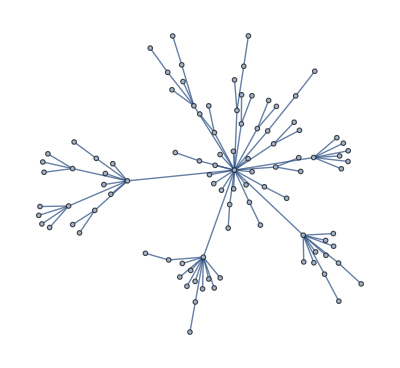

```mathematica
acg=EdgeDelete[g,IGFeedbackArcSet[g]]
```

And try out a few of igraph’s layout algorithms.

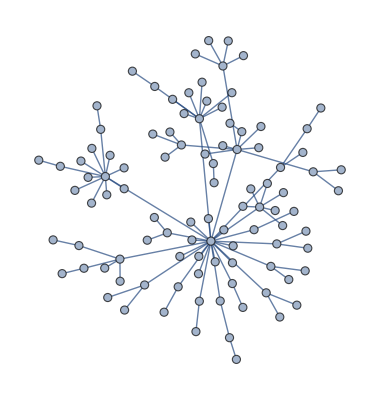
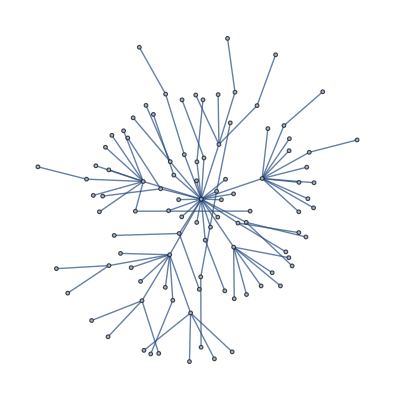
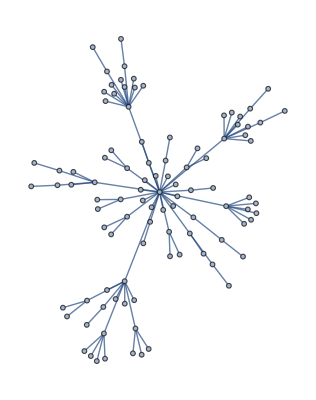

```mathematica
{IGLayoutGraphOpt[acg],IGLayoutKamadaKawai[acg],IGLayoutFruchtermanReingold[acg]}
```

Layout functions typically have many options to tune:

```mathematica
Options[IGLayoutGraphOpt]
```

{MaxIterations→500,NodeCharge→0.001,NodeMass→30,SpringLength→0,SpringConstant→1,MaxStepMovement→5,Continue→False}

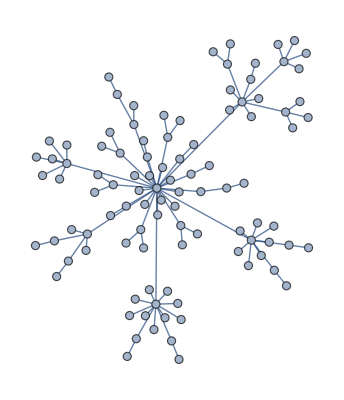

```mathematica
IGLayoutGraphOpt[acg,"MaxIterations"->5000]
```

A final note

Please refer to the usage messages for information on how to use each function. For more information on the meaning of various function options, the algorithms used by the functions, references, etc. please refer to the C/igraph documentation. Note that IGraph/M is currently built using the development version of igraph (0.8.0-pre) while the online igraph documentation is for the last released version (0.7.1). Some new functionality may not be described in the online documentation.

The following sections provide general information on each functionality area, and show common usage patterns.

## Graph creation

All the graph creation functions in IGraph/M take any standard Mathematica Graph option such as VertexLabels, GraphStyle, VertexStyle, etc.

Most included graph creation functions implement random graph models. These use igraph’s (not Mathematica’s) random number generator, which can be re-seeded using IGSeedRandom[].

## Isomorphism

igraph 0.8 implements three isomorphism testing algorithms: BLISS, VF2 and LAD. These support slightly different functionality. Most of IGraph/M’s isomorphism related functions include the name of the algorithm as a prefix, e.g. IGBlissIsomorphicQ. The exceptions are IGIsomorphicQ[] and IGSubisomorphicQ[] which use igraph’s default (VF2 in the current implementation).

### BLISS

See http://www.tcs.hut.fi/Software/bliss/ and http://igraph.org/c/doc/igraph-Isomorphism.html#idm470920858320

The current implementation only supports undirected graphs.

```mathematica
?IGBliss*
```

### VF2

VF2 supports vertex coloured and edge coloured graphs. Colours can be provided as a pair of integer lists using the “VertexColors” or “EdgeColors” options.

```mathematica
?IGVF2*
```

### LAD

See http://liris.cnrs.fr/csolnon/LAD.html and http://igraph.org/c/doc/igraph-Isomorphism.html#idm470934622128

LAD can search for induced subraphs. Use the “Induced” -> True option.

```mathematica
?IGLAD*
```

## Layout algorithms

Most layout algorithms take a “MaxIterations” option. This controls either the maximum number of iterations performed by the algorithm or the exact number of iterations, depending on the specific algorithm the the values of other options. The option name is the same for all functions to make it easier to interchange them when visualizing dynamic graphs.

## Notes on other functions

### Random number generator

igraph’s random number generator can be seeded using

```mathematica
IGSeedRandom[123]
```

### IGData[]

The IGData[] function provides access to various useful datasets. In particular, it can list small directed graphs ordered based on their IGIsoclass[], i.e. the same order motif counting functions use.

```mathematica
IGData[]
```

{{AllDirectedGraphs,3},{AllDirectedGraphs,4}}

Here’s all size 3 directed graphs.

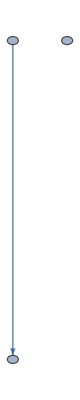
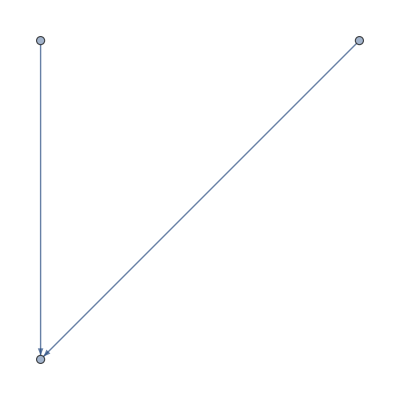
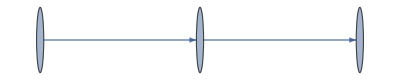
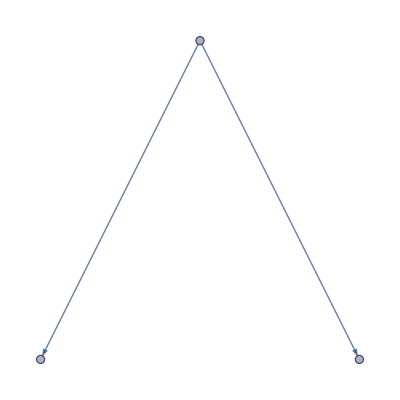
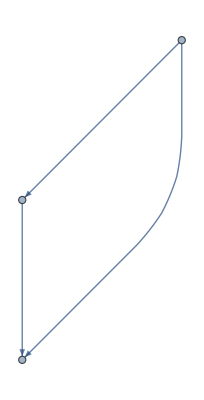
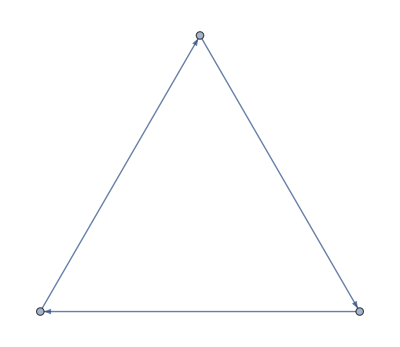
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row@IGData[{"AllDirectedGraphs",3}]
```